## The main part

```mathematica
TheSize=5;
```

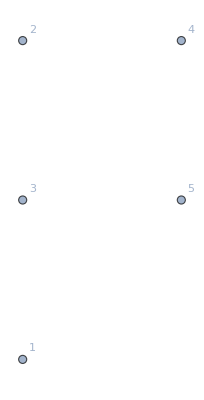

```mathematica
allGraphs=Association[];
g=Graph[Range[TheSize],{}];
Graph[g,VertexLabels->"Name"]
```

```mathematica
mat = MatrixFromGraph[g]
```

{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}}

```mathematica
MatrixForm[mat]
```

(2 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2)

```mathematica
FileName="d:\\Saved\\complete"<>ToString[TheSize]<>".m";
If[FileExistsQ[FileName],
Print["Loading ... ", FileName];
allGraphs=Get[FileName],
Timing[Monitor[ComputeGraph[mat,32],{globalDepth,Length[allGraphs]}]];
Put[allGraphs,FileName]
];
Length[allGraphs]
```

Loading ... d:\Saved\complete5.m

1895

```mathematica
TableForm[Sort[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,Keys[allGraphs]]//Tally],TableDepth->2]
```

{1,Greater} | 1
{2,Greater} | 25
{2,GreaterEqual} | 5
{3,Greater} | 170
{3,GreaterEqual} | 30
{4,Greater} | 560
{4,GreaterEqual} | 80
{5,Equal} | 1
{5,Greater} | 938
{5,GreaterEqual} | 85

```mathematica
TableForm[Sort[Map[{EdgeCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,Keys[allGraphs]]//Tally],TableDepth->2]
```

{0,Greater} | 52
{1,Greater} | 150
{1,GreaterEqual} | 10
{2,Greater} | 260
{2,GreaterEqual} | 10
{3,Greater} | 320
{3,GreaterEqual} | 25
{4,Greater} | 325
{4,GreaterEqual} | 35
{5,Greater} | 287
{5,GreaterEqual} | 25
{6,Greater} | 205
{6,GreaterEqual} | 15
{7,Greater} | 85
{7,GreaterEqual} | 35
{8,Greater} | 10
{8,GreaterEqual} | 35
{9,GreaterEqual} | 10
{10,Equal} | 1

```mathematica
atomKeys=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[atomKeys]
```

52

```mathematica
PrimePi[52]
```

15

```mathematica
atomSymbols=Table[allGraphs[k,"colofour"],{k,atomKeys}];Length[atomSymbols]
```

52

```mathematica
TableForm[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,atomKeys]//Tally//Sort,TableDepth->2]
```

{1,Greater} | 1
{2,Greater} | 10
{2,GreaterEqual} | 5
{3,Greater} | 10
{3,GreaterEqual} | 15
{4,GreaterEqual} | 10
{5,Equal} | 1

```mathematica
TableForm[Map[{EdgeCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,atomKeys]//Tally//Sort,TableDepth->2]
```

{0,Greater} | 1
{1,Greater} | 10
{1,GreaterEqual} | 5
{3,Greater} | 10
{3,GreaterEqual} | 15
{6,GreaterEqual} | 10
{10,Equal} | 1

```mathematica
allGraphs[0,"graph"]
```

-Graphics-

```mathematica
TableForm[Table[{k,allGraphs[k,"graph"],ChromaticPolynomial[allGraphs[k,"graph"],x]//Factor,ChromaticPolynomial[allGraphs[k,"graph"],x],ChromaticPolynomial[allGraphs[k,"graph"],4]},{k,atomKeys}],TableDepth->2];
```

```mathematica
repZero=Sort[Map[allGraphs[#,"colofour"]->0&,Select[Keys[allGraphs],ToString[allGraphs[#,"comp"]]=="Equal"&&Length[DeleteDuplicates[ListofVars[allGraphs[#,"colofour"]]]]==1&]]];Length[repZero]
```

1

```mathematica
repcolofourtextBase2=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]],{k,atomKeys}];
```

```mathematica
Take[repcolofourtextBase2,-20]
```

{v135x2x4→v135x2x4,v135x24→v135x24,v134x2x5→v134x2x5,v134x25→v134x25,v1345x2→v1345x2,v12x3x4x5→v12x3x4x5,v12x3x45→v12x3x45,v12x35x4→v12x35x4,v12x34x5→v12x34x5,v12x345→v12x345,v125x3x4→v125x3x4,v125x34→v125x34,v124x3x5→v124x3x5,v124x35→v124x35,v1245x3→v1245x3,v123x4x5→v123x4x5,v123x45→v123x45,v1235x4→v1235x4,v1234x5→v1234x5,v12345→v12345}

```mathematica
repcolofourgraph2=Table[allGraphs[k,"colofour"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}],FrameStyle->Directive[Blue]],{k,atomKeys}];
```

```mathematica
demoValues={v1x2x3x4x5->0,v1x2x3x45->53,v1x2x35x4->30,v1x2x34x5->54,v1x2x345->87,v1x25x3x4->41,v1x25x34->64,v1x24x3x5->27,v1x24x35->16,v1x245x3->35,v1x23x4x5->74,v1x23x45->74,v1x235x4->33,v1x234x5->101,v1x2345->63,v15x2x3x4->58,v15x2x34->119,v15x24x3->74,v15x23x4->115,v15x234->102,v14x2x3x5->52,v14x2x35->41,v14x25x3->52,v14x23x5->101,v14x235->30,v145x2x3->177,v145x23->143,v13x2x4x5->72,v13x2x45->74,v13x25x4->72,v13x24x5->58,v13x245->28,v135x2x4->40,v135x24->28,v134x2x5->66,v134x25->38,v1345x2->68,v12x3x4x5->82,v12x3x45->90,v12x35x4->53,v12x34x5->133,v12x345->78,v125x3x4->121,v125x34->95,v124x3x5->79,v124x35->25,v1245x3->68,v123x4x5->202,v123x45->102,v1235x4->68,v1234x5->104,v12345->68}
```

{v1x2x3x4x5→0,v1x2x3x45→53,v1x2x35x4→30,v1x2x34x5→54,v1x2x345→87,v1x25x3x4→41,v1x25x34→64,v1x24x3x5→27,v1x24x35→16,v1x245x3→35,v1x23x4x5→74,v1x23x45→74,v1x235x4→33,v1x234x5→101,v1x2345→63,v15x2x3x4→58,v15x2x34→119,v15x24x3→74,v15x23x4→115,v15x234→102,v14x2x3x5→52,v14x2x35→41,v14x25x3→52,v14x23x5→101,v14x235→30,v145x2x3→177,v145x23→143,v13x2x4x5→72,v13x2x45→74,v13x25x4→72,v13x24x5→58,v13x245→28,v135x2x4→40,v135x24→28,v134x2x5→66,v134x25→38,v1345x2→68,v12x3x4x5→82,v12x3x45→90,v12x35x4→53,v12x34x5→133,v12x345→78,v125x3x4→121,v125x34→95,v124x3x5→79,v124x35→25,v1245x3→68,v123x4x5→202,v123x45→102,v1235x4→68,v1234x5→104,v12345→68}

## Now we look at the polynomials

```mathematica
ChromaticPolynomial[allGraphs[alfa1Key,"graph"],x]//Factor
```

(-2+x) (-1+x) x

```mathematica
repAtoms=Table[allGraphs[k,"colofour"]->Factor[ChromaticPolynomial[allGraphs[k,"graph"],x]*allGraphs[k,"colofour"]],{k,atomKeys}]
```

{v1x2x3x4x5→v1x2x3x4x5 (-4+x) (-3+x) (-2+x) (-1+x) x,v1x2x3x45→v1x2x3x45 (-3+x) (-2+x) (-1+x) x,v1x2x35x4→v1x2x35x4 (-3+x) (-2+x) (-1+x) x,v1x2x34x5→v1x2x34x5 (-3+x) (-2+x) (-1+x) x,v1x2x345→v1x2x345 (-2+x) (-1+x) x,v1x25x3x4→v1x25x3x4 (-3+x) (-2+x) (-1+x) x,v1x25x34→v1x25x34 (-2+x) (-1+x) x,v1x24x3x5→v1x24x3x5 (-3+x) (-2+x) (-1+x) x,v1x24x35→v1x24x35 (-2+x) (-1+x) x,v1x245x3→v1x245x3 (-2+x) (-1+x) x,v1x23x4x5→v1x23x4x5 (-3+x) (-2+x) (-1+x) x,v1x23x45→v1x23x45 (-2+x) (-1+x) x,v1x235x4→v1x235x4 (-2+x) (-1+x) x,v1x234x5→v1x234x5 (-2+x) (-1+x) x,v1x2345→v1x2345 (-1+x) x,v15x2x3x4→v15x2x3x4 (-3+x) (-2+x) (-1+x) x,v15x2x34→v15x2x34 (-2+x) (-1+x) x,v15x24x3→v15x24x3 (-2+x) (-1+x) x,v15x23x4→v15x23x4 (-2+x) (-1+x) x,v15x234→v15x234 (-1+x) x,v14x2x3x5→v14x2x3x5 (-3+x) (-2+x) (-1+x) x,v14x2x35→v14x2x35 (-2+x) (-1+x) x,v14x25x3→v14x25x3 (-2+x) (-1+x) x,v14x23x5→v14x23x5 (-2+x) (-1+x) x,v14x235→v14x235 (-1+x) x,v145x2x3→v145x2x3 (-2+x) (-1+x) x,v145x23→v145x23 (-1+x) x,v13x2x4x5→v13x2x4x5 (-3+x) (-2+x) (-1+x) x,v13x2x45→v13x2x45 (-2+x) (-1+x) x,v13x25x4→v13x25x4 (-2+x) (-1+x) x,v13x24x5→v13x24x5 (-2+x) (-1+x) x,v13x245→v13x245 (-1+x) x,v135x2x4→v135x2x4 (-2+x) (-1+x) x,v135x24→v135x24 (-1+x) x,v134x2x5→v134x2x5 (-2+x) (-1+x) x,v134x25→v134x25 (-1+x) x,v1345x2→v1345x2 (-1+x) x,v12x3x4x5→v12x3x4x5 (-3+x) (-2+x) (-1+x) x,v12x3x45→v12x3x45 (-2+x) (-1+x) x,v12x35x4→v12x35x4 (-2+x) (-1+x) x,v12x34x5→v12x34x5 (-2+x) (-1+x) x,v12x345→v12x345 (-1+x) x,v125x3x4→v125x3x4 (-2+x) (-1+x) x,v125x34→v125x34 (-1+x) x,v124x3x5→v124x3x5 (-2+x) (-1+x) x,v124x35→v124x35 (-1+x) x,v1245x3→v1245x3 (-1+x) x,v123x4x5→v123x4x5 (-2+x) (-1+x) x,v123x45→v123x45 (-1+x) x,v1235x4→v1235x4 (-1+x) x,v1234x5→v1234x5 (-1+x) x,v12345→v12345 x}

```mathematica
(*repAtoms=Select[repAtoms,!MemberQ[Table[allGraphs[k,"colofour"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}],#[[1]]]&];
```

```mathematica
(*repAtoms=Join[repAtoms,Table[allGraphs[k,"colofour"]->ChromaticPolynomial[allGraphs[k,"graph"],x]*allGraphs[k,"colofour"](x-3),{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]
```

```mathematica
allGraphs[lambdaKey,"colofour"]
```

v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5

```mathematica
(allGraphs[0,"colofour"]/.{v1x2x3x4x5->0}/.repAtoms)/.repcolofourtextBase2//Factor
```

x (v12345-v1234x5+x v1234x5-v1235x4+x v1235x4-v123x45+x v123x45+2 v123x4x5-3 x v123x4x5+x^2 v123x4x5-v1245x3+x v1245x3-v124x35+x v124x35+2 v124x3x5-3 x v124x3x5+x^2 v124x3x5-v125x34+x v125x34+2 v125x3x4-3 x v125x3x4+x^2 v125x3x4-v12x345+x v12x345+2 v12x34x5-3 x v12x34x5+x^2 v12x34x5+2 v12x35x4-3 x v12x35x4+x^2 v12x35x4+2 v12x3x45-3 x v12x3x45+x^2 v12x3x45-6 v12x3x4x5+11 x v12x3x4x5-6 x^2 v12x3x4x5+x^3 v12x3x4x5-v1345x2+x v1345x2-v134x25+x v134x25+2 v134x2x5-3 x v134x2x5+x^2 v134x2x5-v135x24+x v135x24+2 v135x2x4-3 x v135x2x4+x^2 v135x2x4-v13x245+x v13x245+2 v13x24x5-3 x v13x24x5+x^2 v13x24x5+2 v13x25x4-3 x v13x25x4+x^2 v13x25x4+2 v13x2x45-3 x v13x2x45+x^2 v13x2x45-6 v13x2x4x5+11 x v13x2x4x5-6 x^2 v13x2x4x5+x^3 v13x2x4x5-v145x23+x v145x23+2 v145x2x3-3 x v145x2x3+x^2 v145x2x3-v14x235+x v14x235+2 v14x23x5-3 x v14x23x5+x^2 v14x23x5+2 v14x25x3-3 x v14x25x3+x^2 v14x25x3+2 v14x2x35-3 x v14x2x35+x^2 v14x2x35-6 v14x2x3x5+11 x v14x2x3x5-6 x^2 v14x2x3x5+x^3 v14x2x3x5-v15x234+x v15x234+2 v15x23x4-3 x v15x23x4+x^2 v15x23x4+2 v15x24x3-3 x v15x24x3+x^2 v15x24x3+2 v15x2x34-3 x v15x2x34+x^2 v15x2x34-6 v15x2x3x4+11 x v15x2x3x4-6 x^2 v15x2x3x4+x^3 v15x2x3x4-v1x2345+x v1x2345+2 v1x234x5-3 x v1x234x5+x^2 v1x234x5+2 v1x235x4-3 x v1x235x4+x^2 v1x235x4+2 v1x23x45-3 x v1x23x45+x^2 v1x23x45-6 v1x23x4x5+11 x v1x23x4x5-6 x^2 v1x23x4x5+x^3 v1x23x4x5+2 v1x245x3-3 x v1x245x3+x^2 v1x245x3+2 v1x24x35-3 x v1x24x35+x^2 v1x24x35-6 v1x24x3x5+11 x v1x24x3x5-6 x^2 v1x24x3x5+x^3 v1x24x3x5+2 v1x25x34-3 x v1x25x34+x^2 v1x25x34-6 v1x25x3x4+11 x v1x25x3x4-6 x^2 v1x25x3x4+x^3 v1x25x3x4+2 v1x2x345-3 x v1x2x345+x^2 v1x2x345-6 v1x2x34x5+11 x v1x2x34x5-6 x^2 v1x2x34x5+x^3 v1x2x34x5-6 v1x2x35x4+11 x v1x2x35x4-6 x^2 v1x2x35x4+x^3 v1x2x35x4-6 v1x2x3x45+11 x v1x2x3x45-6 x^2 v1x2x3x45+x^3 v1x2x3x45)

```mathematica
Simplify[(v13x24x5+v13x25x4-3 v13x2x4x5+x v13x2x4x5+v14x25x3+v14x2x35-3 v14x2x3x5+x v14x2x3x5+v1x24x35-3 v1x24x3x5+x v1x24x3x5-3 v1x25x3x4+x v1x25x3x4-3 v1x2x35x4+x v1x2x35x4)]
```

v13x24x5+v13x25x4-3 v13x2x4x5+v14x25x3+v14x2x35-3 v14x2x3x5+v1x24x35-3 v1x24x3x5-3 v1x25x3x4-3 v1x2x35x4+v13x2x4x5 x+v14x2x3x5 x+v1x24x3x5 x+v1x25x3x4 x+v1x2x35x4 x

```mathematica
PolynomialReduce[(-4 v13x24x5+x v13x24x5-4 v13x25x4+x v13x25x4+v13x2x4x5-4 v14x25x3+x v14x25x3-4 v14x2x35+x v14x2x35+v14x2x3x5-4 v1x24x35+x v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4),{1},{x}]
```

{{-4 v13x24x5-4 v13x25x4+v13x2x4x5-4 v14x25x3-4 v14x2x35+v14x2x3x5-4 v1x24x35+x (v13x24x5+v13x25x4+v14x25x3+v14x2x35+v1x24x35)+v1x24x3x5+v1x25x3x4+v1x2x35x4},0}

```mathematica
(allGraphs[lambdaKey,"colofour"]/.repAtoms)
```

v13x24x5 (-2+x) (-1+x) x+v13x25x4 (-2+x) (-1+x) x+v14x25x3 (-2+x) (-1+x) x+v14x2x35 (-2+x) (-1+x) x+v1x24x35 (-2+x) (-1+x) x+v13x2x4x5 (-3+x) (-2+x) (-1+x) x+v14x2x3x5 (-3+x) (-2+x) (-1+x) x+v1x24x3x5 (-3+x) (-2+x) (-1+x) x+v1x25x3x4 (-3+x) (-2+x) (-1+x) x+v1x2x35x4 (-3+x) (-2+x) (-1+x) x+v1x2x3x4x5 (-4+x) (-3+x) (-2+x) (-1+x) x

```mathematica
PolynomialReduce[(allGraphs[lambdaKey,"colofour"]/.{v1x2x3x4x5->0}/.repAtoms),{x},{x}]/.repcolofourtextBase2
```

{{2 v13x24x5+2 v13x25x4-6 v13x2x4x5+2 v14x25x3+2 v14x2x35-6 v14x2x3x5+2 v1x24x35-6 v1x24x3x5-6 v1x25x3x4+x^2 (v13x24x5+v13x25x4-6 v13x2x4x5+v14x25x3+v14x2x35-6 v14x2x3x5+v1x24x35-6 v1x24x3x5-6 v1x25x3x4-6 v1x2x35x4)-6 v1x2x35x4+x^3 (v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x35x4)+x (-3 v13x24x5-3 v13x25x4+11 v13x2x4x5-3 v14x25x3-3 v14x2x35+11 v14x2x3x5-3 v1x24x35+11 v1x24x3x5+11 v1x25x3x4+11 v1x2x35x4)},0}

```mathematica
Reduce[Discriminant[First[PolynomialReduce[(allGraphs[lambdaKey,"colofour"]/.{v1x2x3x4x5->0}/.repAtoms),{x},{x}]],x]>0]
```

(v13x25x4|v14x25x3|v14x2x35|v14x2x3x5|v1x24x35|v1x24x3x5|v1x25x3x4|v1x2x35x4)∈Reals&&((v13x2x4x5<-v14x2x3x5-v1x24x3x5-v1x25x3x4-v1x2x35x4&&(v13x24x5<-v13x25x4+2 v13x2x4x5-v14x25x3-v14x2x35+2 v14x2x3x5-v1x24x35+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x35x4||-v13x25x4+2 v13x2x4x5-v14x25x3-v14x2x35+2 v14x2x3x5-v1x24x35+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x35x4<v13x24x5<-v13x25x4+v13x2x4x5-v14x25x3-v14x2x35+v14x2x3x5-v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4||v13x24x5>-v13x25x4+v13x2x4x5-v14x25x3-v14x2x35+v14x2x3x5-v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4))||(v13x2x4x5==-v14x2x3x5-v1x24x3x5-v1x25x3x4-v1x2x35x4&&(v13x24x5<-v13x25x4+2 v13x2x4x5-v14x25x3-v14x2x35+2 v14x2x3x5-v1x24x35+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x35x4||v13x24x5>-v13x25x4+2 v13x2x4x5-v14x25x3-v14x2x35+2 v14x2x3x5-v1x24x35+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x35x4))||(v13x2x4x5>-v14x2x3x5-v1x24x3x5-v1x25x3x4-v1x2x35x4&&(v13x24x5<-v13x25x4+v13x2x4x5-v14x25x3-v14x2x35+v14x2x3x5-v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4||-v13x25x4+v13x2x4x5-v14x25x3-v14x2x35+v14x2x3x5-v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4<v13x24x5<-v13x25x4+2 v13x2x4x5-v14x25x3-v14x2x35+2 v14x2x3x5-v1x24x35+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x35x4||v13x24x5>-v13x25x4+2 v13x2x4x5-v14x25x3-v14x2x35+2 v14x2x3x5-v1x24x35+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x35x4)))

```mathematica
2 v13x24x5+2 v13x25x4-6 v13x2x4x5+2 v14x25x3+2 v14x2x35-6 v14x2x3x5+2 v1x24x35-6 v1x24x3x5-6 v1x25x3x4-6 v1x2x35x4+24 v1x2x3x4x5+(-3 v13x24x5-3 v13x25x4+11 v13x2x4x5-3 v14x25x3-3 v14x2x35+11 v14x2x3x5-3 v1x24x35+11 v1x24x3x5+11 v1x25x3x4+11 v1x2x35x4-50 v1x2x3x4x5) x+(v13x24x5+v13x25x4-6 v13x2x4x5+v14x25x3+v14x2x35-6 v14x2x3x5+v1x24x35-6 v1x24x3x5-6 v1x25x3x4-6 v1x2x35x4+35 v1x2x3x4x5) x^2+(v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x35x4-10 v1x2x3x4x5) x^3+v1x2x3x4x5 x^4/.x->4//Simplify
```

6 (v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4)

## Now the empty graph base

```mathematica
PartitionToNullSymbol[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["p"<>end]]
```

```mathematica
GenerateNullEquations[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
With[{key=First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]},
PartitionToNullSymbol[part]==allGraphs[key,"colofour"]
],
{part,allPartitions}],part]
]
```

```mathematica
repNullBase=Map[#[[1]]->#[[2]]&,AndToTable[Reduce[GenerateNullEquations[allGraphs,5],Table[allGraphs[k,"colofour"],{k,atomKeys}]]]];
```

```mathematica
Monitor[Table[allGraphs[k,"colofournull"]=Simplify[allGraphs[k,"colofour"]/.repNullBase],{k,Keys[allGraphs]}],k];
```

```mathematica
nullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofournull"]]]==1&]];Length[nullAtomKeys]
```

52

```mathematica
nullAtomSymbols=Table[allGraphs[k,"colofournull"],{k,nullAtomKeys}]
```

{p1x2x3x4x5,p1x2x3x45,p1x2x35x4,p1x2x34x5,p1x2x345,p1x25x3x4,p1x25x34,p1x24x3x5,p1x24x35,p1x245x3,p1x23x4x5,p1x23x45,p1x235x4,p1x234x5,p1x2345,p15x2x3x4,p15x2x34,p15x24x3,p15x23x4,p15x234,p14x2x3x5,p14x2x35,p14x25x3,p14x23x5,p14x235,p145x2x3,p145x23,p13x2x4x5,p13x2x45,p13x25x4,p13x24x5,p13x245,p135x2x4,p135x24,p134x2x5,p134x25,p1345x2,p12x3x4x5,p12x3x45,p12x35x4,p12x34x5,p12x345,p125x3x4,p125x34,p124x3x5,p124x35,p1245x3,p123x4x5,p123x45,p1235x4,p1234x5,p12345}

```mathematica
repnullcolofourtextBase2=Table[allGraphs[k,"colofournull"]->Style[allGraphs[k,"colofournull"],ColourForKey[allGraphs,k]],{k,nullAtomKeys}];
```

```mathematica
repcolofournullgraph2=Table[allGraphs[k,"colofournull"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofournull"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}],FrameStyle->Directive[Red,Dotted,Thick]],{k,nullAtomKeys}];
```

```mathematica
repcolofournullgraphsmall=Table[allGraphs[k,"colofournull"]->Framed[Labeled[Graph[allGraphs[k,"graph"],ImageSize->{30,30},VertexLabelStyle->Directive[6]],{Style[allGraphs[k,"colofournull"],Bold,8],Style[k,ColourForKey[allGraphs,k],8]},{Top,Bottom},Spacings->{0,0}],FrameStyle->Directive[Red,Dotted]],{k,nullAtomKeys}];Take[repcolofournullgraphsmall,3]
```

{p1x2x3x4x5→-Graphics-p1x2x3x4x50,p1x2x3x45→-Graphics-p1x2x3x451,p1x2x35x4→-Graphics-p1x2x35x43}

## Playing with the empty graph base

```mathematica
DeleteDuplicates[Flatten[Table[ListofVars[allGraphs[k,"colofournull"]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]]//Length
```

51

```mathematica
(Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify)/.repnullcolofourtextBase2
```

1/12 (5 p12345-3 p1234x5-3 p1235x4-5 p123x45+6 p123x4x5-3 p1245x3+7 p124x35-6 p124x3x5-5 p125x34+6 p125x3x4-5 p12x345+8 p12x34x5-4 p12x35x4+8 p12x3x45-6 p12x3x4x5-3 p1345x2+7 p134x25-6 p134x2x5+7 p135x24-6 p135x2x4+7 p13x245-4 p13x24x5-4 p13x25x4-4 p13x2x45+6 p13x2x4x5-5 p145x23+6 p145x2x3+7 p14x235-4 p14x23x5-4 p14x25x3-4 p14x2x35+6 p14x2x3x5-5 p15x234+8 p15x23x4-4 p15x24x3+8 p15x2x34-6 p15x2x3x4-3 p1x2345+6 p1x234x5-6 p1x235x4+8 p1x23x45-6 p1x23x4x5-6 p1x245x3-4 p1x24x35+6 p1x24x3x5-4 p1x25x34+6 p1x25x3x4+6 p1x2x345-6 p1x2x34x5+6 p1x2x35x4-6 p1x2x3x45)

```mathematica
(Total[Table[allGraphs[k,"colofournull"],{k,{36085,31711,29605,29551,29527}}]]//Simplify)/.repnullcolofourtextBase2
```

1/4 (-5 p12345+p1234x5+p1235x4+3 p123x45-2 p123x4x5+p1245x3-3 p124x35+2 p124x3x5+3 p125x34-2 p125x3x4+3 p12x345-2 p12x34x5-2 p12x3x45+2 p12x3x4x5+p1345x2-3 p134x25+2 p134x2x5-3 p135x24+2 p135x2x4-3 p13x245+2 p13x24x5+2 p13x25x4-2 p13x2x4x5+3 p145x23-2 p145x2x3-3 p14x235+2 p14x25x3+2 p14x2x35-2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x2x34+2 p15x2x3x4+p1x2345-2 p1x234x5+2 p1x235x4-2 p1x23x45+2 p1x23x4x5+2 p1x245x3+2 p1x24x35-2 p1x24x3x5-2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5-2 p1x2x35x4+2 p1x2x3x45)

```mathematica
allGraphs[lambdaKey,"colofournull"]/.repnullcolofourtextBase2
```

1/6 (p12345+2 p123x45-p124x35+2 p125x34+2 p12x345+p12x34x5-2 p12x35x4+p12x3x45-p134x25-p135x24-p13x245+p13x24x5+p13x25x4-2 p13x2x45+2 p145x23-p14x235-2 p14x23x5+p14x25x3+p14x2x35+2 p15x234+p15x23x4-2 p15x24x3+p15x2x34+p1x23x45+p1x24x35-2 p1x25x34)

```mathematica
Length[Intersection[Simplify[allGraphs[alfa1Key,"colofournull"]==0]//ListofVars,Simplify[allGraphs[36085,"colofournull"]==0]//ListofVars]]
```

34

```mathematica
Simplify[allGraphs[lambdaKey,"colofournull"]==0]/.repcolofournullgraph2
```

-Graphics-p12x34x519692+-Graphics-p12x3x4519684+-Graphics-p13x24x56642+-Graphics-p13x25x46588+-Graphics-p14x25x32214+-Graphics-p14x2x352190+-Graphics-p15x23x4972+-Graphics-p15x2x34738+-Graphics-p1x23x45244+-Graphics-p1x24x3584+2 -Graphics-p123x4526488+2 -Graphics-p125x3420448+2 -Graphics-p12x34519696+2 -Graphics-p145x233160+2 -Graphics-p15x2341062+-Graphics-p1234529524==2 -Graphics-p12x35x419686+2 -Graphics-p13x2x456562+2 -Graphics-p14x23x52430+2 -Graphics-p15x24x3810+2 -Graphics-p1x25x3436+-Graphics-p124x3521954+-Graphics-p134x258784+-Graphics-p135x247374+-Graphics-p13x2456670+-Graphics-p14x2352460

## Inequalities de

```mathematica
ineqsnull=Table[allGraphs[k,"comp"][allGraphs[k,"colofournull"],0],{k,Keys[allGraphs]}];
```

```mathematica
baseZero=Table[allGraphs[k,"colofournull"]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}];
```

```mathematica
nullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofournull"],0],{k,nullAtomKeys}];Length[nullAtomFacts]
```

52

```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofour"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

1895

```mathematica
atomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,atomKeys}];Length[atomFacts]
```

52

```mathematica
links = Table[allGraphs[k,"colofour"]==allGraphs[k,"colofournull"],{k,Keys[allGraphs]}];Length[links]
```

1895

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
(*ineqsnullSimp=Monitor[Simplify[Fold[And,Join[ineqsnull,ineqs,links]],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->Join[atomFacts,nullAtomFacts]],countDone];Length[ineqsnullSimp]*)
```

```mathematica
(*ExpressionToTable[Select[ineqsnullSimp,1<=Length[#[[1]]]+Length[#[[2]]]≤2&]/.repZero]/.repcolofournullgraph2*)
```

```mathematica
(*(Select[AndToTable[ineqsnullSimp],With[{v=ListofVars[#]},8<Length[#[[1]]]+Length[#[[2]]]≤10&&(Length[Intersection[v,nullAtomSymbols]]>0)&&(Length[Intersection[v,atomSymbols]]>0)]&])/.repcolofourgraph2/.repcolofournullgraph2*)
```

```mathematica
(*TableForm[Tally[Table[With[{v=DeleteDuplicates[ListofVars[ineqsnullSimp[[k]]]]},{Length[ineqsnullSimp[[k,1]]]+Length[ineqsnullSimp[[k,2]]],(Length[Intersection[v,nullAtomSymbols]]),(Length[Intersection[v,atomSymbols]])}],{k,Length[ineqsnullSimp]}]]//Sort, TableDepth->2]*)
```

## See what we can get for the special graphs

```mathematica
specialAtomSymbols=Table[allGraphs[k,"colofour"],{k,{36085,31711,29605,29551,29527,alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{v13x2x4x5,v14x2x3x5,v1x24x3x5,v1x25x3x4,v1x2x35x4,v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
forcedZero=Fold[And,Table[allGraphs[k,"colofour"]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]
```

v13x24x5==0&&v14x25x3==0&&v1x24x35==0&&v13x25x4==0&&v14x2x35==0

```mathematica
Length[ineqsnullSimp]
```

244

```mathematica
countDone=0;ineqsnullSimp2=Monitor[Simplify[ineqsnullSimp&&forcedZero,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->Join[atomFacts,nullAtomFacts]],countDone];
```

```mathematica
filtered=Select[AndToTable[ineqsnullSimp2],With[{vars=ListofVars[#]},Length[vars]<50&&Length[Intersection[vars,specialAtomSymbols]]>0]&];Length[filtered]
```

5

```mathematica
Take[filtered,3]
```

{v13x24x5==0,v14x25x3==0,v1x24x35==0}

```mathematica
(*Reduce[Fold[And,filtered],specialAtomSymbols]*)
```

## Taking formula fro empty graph combined with all full

```mathematica
allGraphs[0,"colofour"]//Length
```

52

```mathematica
repElim=Table[Solve[allGraphs[0,"colofournull"]==allGraphs[0,"colofour"],allGraphs[k,"colofour"]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Flatten
```

{v13x24x5→p1x2x3x4x5-v12345-v1234x5-v1235x4-v123x45-v123x4x5-v1245x3-v124x35-v124x3x5-v125x34-v125x3x4-v12x345-v12x34x5-v12x35x4-v12x3x45-v12x3x4x5-v1345x2-v134x25-v134x2x5-v135x24-v135x2x4-v13x245-v13x25x4-v13x2x45-v13x2x4x5-v145x23-v145x2x3-v14x235-v14x23x5-v14x25x3-v14x2x35-v14x2x3x5-v15x234-v15x23x4-v15x24x3-v15x2x34-v15x2x3x4-v1x2345-v1x234x5-v1x235x4-v1x23x45-v1x23x4x5-v1x245x3-v1x24x35-v1x24x3x5-v1x25x34-v1x25x3x4-v1x2x345-v1x2x34x5-v1x2x35x4-v1x2x3x45-v1x2x3x4x5,v14x25x3→p1x2x3x4x5-v12345-v1234x5-v1235x4-v123x45-v123x4x5-v1245x3-v124x35-v124x3x5-v125x34-v125x3x4-v12x345-v12x34x5-v12x35x4-v12x3x45-v12x3x4x5-v1345x2-v134x25-v134x2x5-v135x24-v135x2x4-v13x245-v13x24x5-v13x25x4-v13x2x45-v13x2x4x5-v145x23-v145x2x3-v14x235-v14x23x5-v14x2x35-v14x2x3x5-v15x234-v15x23x4-v15x24x3-v15x2x34-v15x2x3x4-v1x2345-v1x234x5-v1x235x4-v1x23x45-v1x23x4x5-v1x245x3-v1x24x35-v1x24x3x5-v1x25x34-v1x25x3x4-v1x2x345-v1x2x34x5-v1x2x35x4-v1x2x3x45-v1x2x3x4x5,v1x24x35→p1x2x3x4x5-v12345-v1234x5-v1235x4-v123x45-v123x4x5-v1245x3-v124x35-v124x3x5-v125x34-v125x3x4-v12x345-v12x34x5-v12x35x4-v12x3x45-v12x3x4x5-v1345x2-v134x25-v134x2x5-v135x24-v135x2x4-v13x245-v13x24x5-v13x25x4-v13x2x45-v13x2x4x5-v145x23-v145x2x3-v14x235-v14x23x5-v14x25x3-v14x2x35-v14x2x3x5-v15x234-v15x23x4-v15x24x3-v15x2x34-v15x2x3x4-v1x2345-v1x234x5-v1x235x4-v1x23x45-v1x23x4x5-v1x245x3-v1x24x3x5-v1x25x34-v1x25x3x4-v1x2x345-v1x2x34x5-v1x2x35x4-v1x2x3x45-v1x2x3x4x5,v13x25x4→p1x2x3x4x5-v12345-v1234x5-v1235x4-v123x45-v123x4x5-v1245x3-v124x35-v124x3x5-v125x34-v125x3x4-v12x345-v12x34x5-v12x35x4-v12x3x45-v12x3x4x5-v1345x2-v134x25-v134x2x5-v135x24-v135x2x4-v13x245-v13x24x5-v13x2x45-v13x2x4x5-v145x23-v145x2x3-v14x235-v14x23x5-v14x25x3-v14x2x35-v14x2x3x5-v15x234-v15x23x4-v15x24x3-v15x2x34-v15x2x3x4-v1x2345-v1x234x5-v1x235x4-v1x23x45-v1x23x4x5-v1x245x3-v1x24x35-v1x24x3x5-v1x25x34-v1x25x3x4-v1x2x345-v1x2x34x5-v1x2x35x4-v1x2x3x45-v1x2x3x4x5,v14x2x35→p1x2x3x4x5-v12345-v1234x5-v1235x4-v123x45-v123x4x5-v1245x3-v124x35-v124x3x5-v125x34-v125x3x4-v12x345-v12x34x5-v12x35x4-v12x3x45-v12x3x4x5-v1345x2-v134x25-v134x2x5-v135x24-v135x2x4-v13x245-v13x24x5-v13x25x4-v13x2x45-v13x2x4x5-v145x23-v145x2x3-v14x235-v14x23x5-v14x25x3-v14x2x3x5-v15x234-v15x23x4-v15x24x3-v15x2x34-v15x2x3x4-v1x2345-v1x234x5-v1x235x4-v1x23x45-v1x23x4x5-v1x245x3-v1x24x35-v1x24x3x5-v1x25x34-v1x25x3x4-v1x2x345-v1x2x34x5-v1x2x35x4-v1x2x3x45-v1x2x3x4x5}

```mathematica
quadBigger=Fold[And,Table[allGraphs[k,"colofour"]>0,{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]
```

v13x2x4x5>0&&v1x24x3x5>0&&v1x2x35x4>0&&v14x2x3x5>0&&v1x25x3x4>0

```mathematica
ListofVars[ineqs]//DeleteDuplicates//Length
```

52

```mathematica
ineqsAnd=Fold[And,ineqs];Length[ineqsAnd]
```

1895

```mathematica
repbaseZero=Table[allGraphs[k,"colofour"]->0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{v13x24x5→0,v14x25x3→0,v1x24x35→0,v13x25x4→0,v14x2x35→0}

```mathematica
workbase=(ineqsAnd/.repElim/.repbaseZero)&&quadBigger;
```

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[#]&,AndToTable[workbase]]]]//Length
```

48

```mathematica
(*countDone=0;ineqsElim=Monitor[Simplify[ineqsAnd/.repElim/.repbaseZero,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->atomFacts],countDone];Length[ineqsElim]*)
```

```mathematica
(*Take[ineqsElim,3]*)
```

```mathematica
(*Sort[Tally[Map[Length[ListofVars[#]]&,AndToTable[ineqsElim]]]]*)
```

```mathematica
(*subset=Select[AndToTable[ineqsElim],Length[ListofVars[#]]==2&]*)
```

```mathematica
(*Select[Keys[allGraphs],allGraphs[#,"colofour"]==v135x2x4+v15x2x3x4&]*)
```

```mathematica
allGraphs[23689,"colofournull"]/.repcolofournullgraph2
```

1/6 (2 -Graphics-p13x2x4x56561-2 -Graphics-p15x2x3x4729-2 -Graphics-p1x23x4x5243+2 -Graphics-p1x24x3x581-2 -Graphics-p1x2x34x59+2 -Graphics-p1x2x35x43+-Graphics-p12x34x519692--Graphics-p12x35x419686-2 -Graphics-p13x24x56642--Graphics-p13x25x46588--Graphics-p13x2x456562+-Graphics-p14x23x52430--Graphics-p14x2x352190+2 -Graphics-p15x23x4972+2 -Graphics-p15x2x34738+-Graphics-p1x23x45244-2 -Graphics-p1x24x3584+-Graphics-p1x25x3436--Graphics-p123x4x526487+-Graphics-p125x3x420439--Graphics-p134x2x58757+-Graphics-p145x2x32917+4 -Graphics-p1x234x5333--Graphics-p1x235x4273--Graphics-p1x2x34513+-Graphics-p123x4526488+-Graphics-p124x3521954-2 -Graphics-p125x3420448+-Graphics-p12x34519696+-Graphics-p134x258784+-Graphics-p135x247374+-Graphics-p13x2456670-2 -Graphics-p145x233160+-Graphics-p14x2352460-5 -Graphics-p15x2341062+-Graphics-p1234x528764--Graphics-p1245x322708+-Graphics-p1x2345364--Graphics-p1234529524)

```mathematica
(*ExpressionToTable[subset]/.repcolofourgraph2*)
```

## Real null base

```mathematica
PartitionToRealNullSymbol[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["n"<>end]]
```

```mathematica
GenerateRealNullEquations[assoc_]:=Block[
{keysWithoutEdges=Select[Keys[assoc],EdgeCount[assoc[#,"graph"]]==0&]},
Table[PartitionToRealNullSymbol[assoc[key,"vertexsets"]]==assoc[key,"colofour"],{key,keysWithoutEdges}]
]
```

```mathematica
eqsRealNull=GenerateRealNullEquations[allGraphs];
```

```mathematica
repRealNullBase=Map[#[[1]]->#[[2]]&,AndToTable[Reduce[GenerateRealNullEquations[allGraphs],Table[allGraphs[k,"colofour"],{k,atomKeys}]]]];
```

```mathematica
Take[repRealNullBase,2]
```

{v1x2x3x4x5→24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,v1x2x3x45→-6 n12345+2 n123x45+2 n1245x3+n12x345-n12x3x45+2 n1345x2+n13x245-n13x2x45+n145x23-n145x2x3+2 n1x2345-n1x23x45-n1x245x3-n1x2x345+n1x2x3x45}

```mathematica
Monitor[Table[allGraphs[k,"colofourrealnull"]=Simplify[allGraphs[k,"colofour"]/.repRealNullBase],{k,Keys[allGraphs]}],k];
```

```mathematica
realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]];Length[realyNullAtomKeys]
```

52

```mathematica
realyNullAtomVars=Table[allGraphs[k,"colofourrealnull"],{k,realyNullAtomKeys}]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x35x4,n1x2x34x5,n1x2x345,n1x25x3x4,n1x25x34,n1x24x3x5,n1x24x35,n1x245x3,n1x23x4x5,n1x23x45,n1x235x4,n1x234x5,n1x2345,n15x2x3x4,n15x2x34,n15x24x3,n15x23x4,n15x234,n14x2x3x5,n14x2x35,n14x25x3,n14x23x5,n14x235,n145x2x3,n145x23,n13x2x4x5,n13x2x45,n13x25x4,n13x24x5,n13x245,n135x2x4,n135x24,n134x2x5,n134x25,n1345x2,n12x3x4x5,n12x3x45,n12x35x4,n12x34x5,n12x345,n125x3x4,n125x34,n124x3x5,n124x35,n1245x3,n123x4x5,n123x45,n1235x4,n1234x5,n12345}

```mathematica
repcolofourrealnullgraph2=Table[allGraphs[k,"colofourrealnull"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofourrealnull"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}],FrameStyle->Directive[Red,Dotted,Thick]],{k,realyNullAtomKeys}];
```

```mathematica
repcolofourrealnullgraphsmall=Table[allGraphs[k,"colofourrealnull"]->Framed[Labeled[Graph[allGraphs[k,"graph"],ImageSize->{30,30},VertexLabelStyle->Directive[6]],{Style[allGraphs[k,"colofourrealnull"],Bold,8],Style[k,ColourForKey[allGraphs,k],8]},{Top,Bottom},Spacings->{0,0}],FrameStyle->Directive[Red,Dotted]],{k,realyNullAtomKeys}];Take[repcolofourrealnullgraphsmall,3]
```

{n1x2x3x4x5→-Graphics-n1x2x3x4x50,n1x2x3x45→-Graphics-n1x2x3x452,n1x2x35x4→-Graphics-n1x2x35x46}

```mathematica
CoeffRealNull[exp_]:=Table[Coefficient[exp,var],{var,Sort[realyNullAtomVars]}]
```

```mathematica
Table[allGraphs[k,"graph"]->CoeffRealNull[allGraphs[k,"colofourrealnull"]]/.repcolofourrealnullgraph2,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//TableForm
```

-Graphics-→{2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
-Graphics-→{2,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
CoeffRealNull[allGraphs[k5Key,"colofourrealnull"]]
```

{24,-6,-6,-2,2,-6,-2,2,-2,2,-2,1,1,1,-1,-6,-2,2,-2,2,-2,1,1,1,-1,-2,2,-2,1,1,1,-1,-2,1,1,1,-1,-6,2,2,1,-1,2,1,-1,1,-1,2,-1,-1,-1,1}

```mathematica
TableForm[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,realyNullAtomKeys]//Tally//Sort,TableDepth->2]
```

{1,Greater} | 1
{2,Greater} | 15
{3,Greater} | 25
{4,Greater} | 10
{5,Greater} | 1

```mathematica
TableForm[Map[{EdgeCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,nullAtomKeys]//Tally//Sort,TableDepth->2]
```

{0,Greater} | 1
{1,Greater} | 10
{2,Greater} | 15
{3,Greater} | 10
{4,Greater} | 10
{6,GreaterEqual} | 5
{10,Equal} | 1